only need to submit exercise 1 and 3

```mathematica
f[x_,y_]=Exp[-(x^2+y^2)]
Plot3D[f[x,y],{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"}]
```

ⅇ^(-x^2-y^2)

-Graphics3D-

```mathematica
f[x_,y_]=Exp[-1/(x^2+y^2)]
```

ⅇ^(-1/(x^2+y^2))

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
f[x_,y_]=x*y/(x^2+y^2)
```

```mathematica
(x y)/(x^2+y^2)
Plot3D[f[x,y],{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"}]
```

(x y)/(x^2+y^2)

-Graphics3D-

```mathematica
Options[Graphics3D];
graph=Plot3D[f[x,y],{x,-1,1},{y,-1,1},Mesh->Automatic,PlotPoints->60];
lines=Graphics3D[{Thickness[0.02],Red,Line[{{-1,-1,.5},{1,1,.5}}],Blue,Line[{{-1,1,-.5},{1,-1,-.5}}]}];
Show[graph,lines,AxesLabel->{"x","y","z"},ViewPoint->{1.3,-2.4,2}]
```

-Graphics3D-

```mathematica
f[x,x]
```

1/2

```mathematica
f[x,-x]
```

-1/2

```mathematica
Clear[g,x,y];
g[x_,y_]=(2x^2 *y)/(x^4+y^2)
 Plot3D[g[x,y],{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"},PlotPoints->60]
```

(2 x^2 y)/(x^4+y^2)

-Graphics3D-

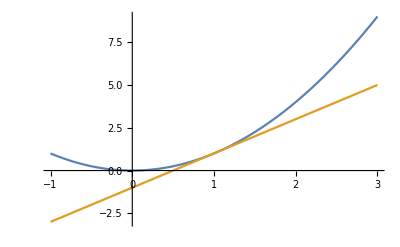

```mathematica
Plot[{x^2,2x-1},{x,-1,3}]
```

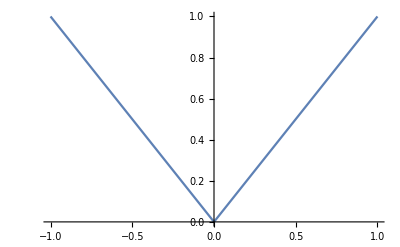

```mathematica
Plot[Abs[x],{x,-1,1}]
```

```mathematica
surf1=Plot3D[Exp[-(x^2+y^2)]-1,{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
surf2=Plot3D[(x^3-y^3)/(x^2+y^2),{x,-1,1},{y,-1,1},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
plane2=Plot3D[x-y,{x,-1,1},{y,-1,1}];
Show[surf2,plane2,BoxRatios->{1,1,2}]
```

-Graphics3D-

```mathematica
plane1=Plot3D[0,{x,-1,1},{y,-1,1}];
Show[surf1,plane1]
```

-Graphics3D-